```mathematica
ClearAll[r]
```

```mathematica
f[x_]=4r*x(1-x)
```

4 r (1-x) x

```mathematica
fPlot[n_]:=Module[{},
Return[ListPlot [ 
NestList[f, 0.5, n],
Joined -> True,
Mesh->All,
Axes -> False, 
Frame -> True, 
FrameLabel -> {"n","x"},  
PlotStyle->Directive[PointSize[Large]]
 ]];
]
```

```mathematica
Rs={0.2,0.7,0.82,0.88,0.97}
```

{0.2,0.7,0.82,0.88,0.97}

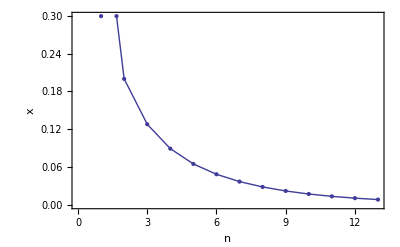
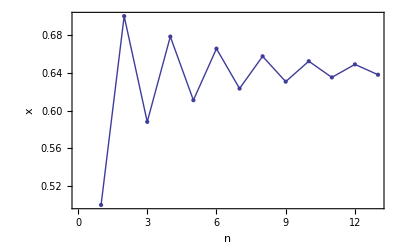
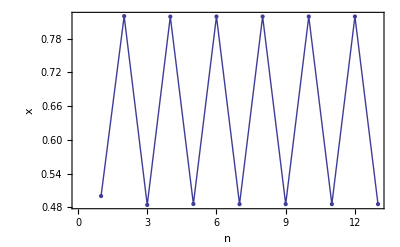
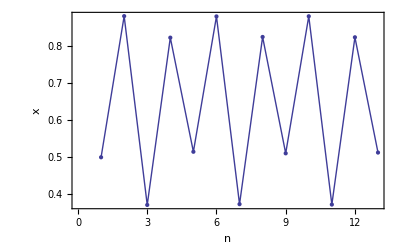
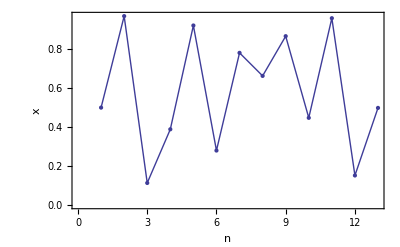

```mathematica
Table[fPlot[12],{r,Rs}]
```

```mathematica
Table[1/2000*Sum[Log[Abs[f'[FixedPoint[f,0.5,i]]]],{i,1,2000}],{r,Rs}]
```

{-0.223941,-0.223215,-0.808696,-0.193043,0.466617}

Only positive when chaotic, i.e. r=0.97

```mathematica
iterator[m_,n_] := Drop[NestList[f,0.5,n],m]
drawpoint[y_] := Point[{r,y}]
```

```mathematica
graph[rmin_,rmax_, nr_, mdrop_, n_] := 
Graphics[ 
{PointSize[0.001],
Table [
 Map[drawpoint, iterator [mdrop,n ] ], 
{r, rmin, rmax, (rmax-rmin)/nr} ]}]
```

```mathematica
Show [ 
graph[0.9340, 0.9360, 400, 300, 700], 
Axes -> False, 
Frame -> True, 
FrameLabel -> {"r", "x"}, 
AspectRatio -> 1 ]
```

-Graphics-

The 5 period cycle can be clearly seen in the center of the plot. At 0.9340 there is chaos.